```mathematica
(*Find a root of the equation x^3+4 x^2-10=0 using fixed point iteration method*)
g[x_]:=(√(10-x^3))/2;
f[x_]:=x^3+4*x^2-10;
s=0;
(Label[1];
a[0]=Input["Enter initial point"];
If[Abs[g'[a[0]]]≥1,{Print["Re-enter the initial point"];
s++;
If[s==3,{Break[],Print["Error"]}];
Goto[1];}];);
n=Input["Enter maximum number of iteration"];
tol=.00001;
k=0;
For[i=1,i≤n,i++,{
k++;
a[i]=g[a[i-1]];
If[Abs[a[i]-a[i-1]]<tol,Break[];]
}];
t=Table[{i,a[i]},{i,0,k}];
PaddedForm[TableForm[t]//N,{13,9}]
If[n==k,Print["Maximum number of iteration"]];
```

0.000000000 |     1.500000000
    1.000000000 |     1.286953768
    2.000000000 |     1.402540804
    3.000000000 |     1.345458374
    4.000000000 |     1.375170253
    5.000000000 |     1.360094193
    6.000000000 |     1.367846968
    7.000000000 |     1.363887004
    8.000000000 |     1.365916733
    9.000000000 |     1.364878217
   10.000000000 |     1.365410061
   11.000000000 |     1.365137821
   12.000000000 |     1.365277209
   13.000000000 |     1.365205850
   14.000000000 |     1.365242384
   15.000000000 |     1.365223680
   16.000000000 |     1.365233256

```mathematica
--
```

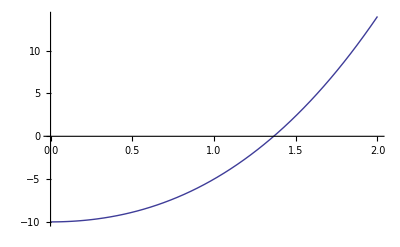

```mathematica
Plot[x^3+4*x^2-10,{x,0,2}]
```